```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
p[l_,α_]:=N[l α+(1-α) IntegerPart[l/(1+α)]];
```

```mathematica
τ=N [(1+Sqrt[5])/2];
t[i_]:=p[i+1,1/τ]-p[i,1/τ]
```

```mathematica
(* rk: t[i] is related to IntegerPart[τ^-1( #+1)]-IntegerPart[τ^-1 #] *)
(IntegerPart[τ^-1( #+1)]-IntegerPart[τ^-1 #])&/@Range[20]
(IntegerPart[τ^-1( #+1)]-IntegerPart[τ^-1 #]-t[#])&/@Range[20]//Chop
```

{1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0}

{0,-0.618034,0,0,-0.618034,0,-0.618034,0,0,-0.618034,0,0,-0.618034,0,-0.618034,0,0,-0.618034,0,-0.618034}

```mathematica
(* hamiltonien avec conditions aux bords libres *)
Clear[h];
h[n_]:=Block[{tbl,ar,Fn},
Fn=Fibonacci[n];
tbl=Table[{i,i+1}->t[i],{i,1,Fn-1}];
ar=SparseArray[tbl,{Fn,Fn}];
Normal[ar+Transpose[ar]]
]
h[6]//MatrixForm
```

(0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 0. | 0.618034 | 0. | 0. | 0. | 0. | 0.
0. | 0.618034 | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.618034 | 0. | 0.
0. | 0. | 0. | 0. | 0.618034 | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.618034
0. | 0. | 0. | 0. | 0. | 0. | 0.618034 | 0.)

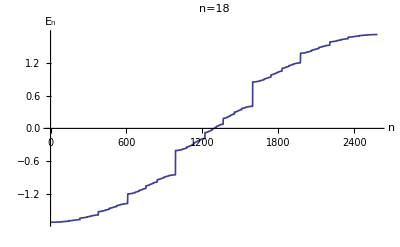

```mathematica
(* spectre *)
Block[{vp,plot,i=18},
vp=Sort[Eigenvalues[h[i]]];
plot=ListPlot[vp,Joined->True,AxesLabel->{"n","E_n"},PlotLabel->"n="<>ToString[i],PlotStyle->Thickness[th]];
Export[dir<>"/data/spectrum_fibo_chain.png",plot];
Print[plot];
]
```